# Колебания струны со свободным концом

Случай 1

```mathematica
a=1;
dt=0.05;
dx=0.1;
```

```mathematica
Clear@func
func[n_]:=Module[{U=Table[Table[0,{x,0,1,dx}],n],l},l=Length[U⟦1⟧];U⟦1⟧=Table[x*(1-x),{x,0,1,dx}]; Do[U⟦2⟧⟦j⟧=U⟦1⟧⟦j⟧*2*(1-(a^2 dt^2)/dx^2)+(a^2 dt^2)/dx^2*(U⟦1⟧⟦j-1⟧+U⟦1⟧⟦j+1⟧),{j,2,l-1}];U⟦2⟧⟦l⟧=U⟦1⟧⟦l-1⟧;Do[Do[U⟦i⟧⟦j⟧=U⟦i-1⟧⟦j⟧*2*(1-(a^2 dt^2)/dx^2)+(a^2 dt^2)/dx^2*(U⟦i-1⟧⟦j-1⟧+U⟦i-1⟧⟦j+1⟧)- U⟦i-2⟧⟦j⟧,{j,2,l-1}];U⟦i⟧⟦l⟧=U⟦i-1⟧⟦l-1⟧,{i,3,n}];U]
```

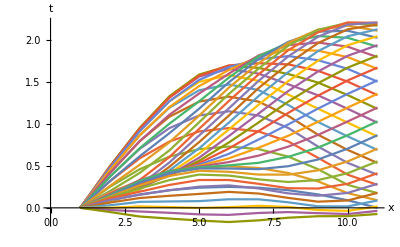

```mathematica
ListLinePlot[func[40],AxesLabel->{"x","t"}
]
```

```mathematica
Animate[ListLinePlot[func[n]⟦-1⟧,PlotRange->{-3,3},Mesh->{{0,11}},MeshStyle->{PointSize[Large],Red}],{n,2,200}]
```

Случай 2

```mathematica
Clear@func2
func2[n_]:=Module[{U=Table[Table[0,{x,0,1,dx}],n],l},l=Length[U⟦1⟧];U⟦1⟧=Table[x*(1-x),{x,0,1,dx}]; Do[U⟦2⟧⟦j⟧=U⟦1⟧⟦j⟧*2*(1-(a^2 dt^2)/dx^2)+(a^2 dt^2)/dx^2*(U⟦1⟧⟦j-1⟧+U⟦1⟧⟦j+1⟧),{j,2,l-1}];U⟦2⟧⟦1⟧=U⟦1⟧⟦2⟧;Do[Do[U⟦i⟧⟦j⟧=U⟦i-1⟧⟦j⟧*2*(1-(a^2 dt^2)/dx^2)+(a^2 dt^2)/dx^2*(U⟦i-1⟧⟦j-1⟧+U⟦i-1⟧⟦j+1⟧)- U⟦i-2⟧⟦j⟧,{j,2,l-1}];U⟦i⟧⟦1⟧=U⟦i-1⟧⟦2⟧,{i,3,n}];U]
```

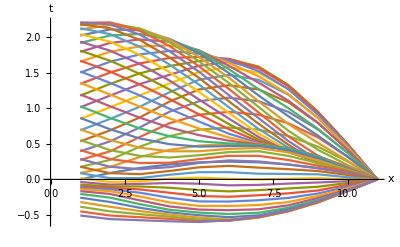

```mathematica
ListLinePlot[func2[50],AxesLabel->{"x","t"}]
```

```mathematica
Animate[ListLinePlot[func2[n]⟦-1⟧,PlotRange->{-3,3},Mesh->{{0,1}},MeshStyle->{PointSize[Large],Red}],{n,2,200}]
```

Случай, когда оба конца закреплены

```mathematica
Clear@func3
func3[n_]:=Module[{U=Table[Table[0,{x,0,1,dx}],n],l},l=Length[U⟦1⟧];U⟦1⟧=Table[x*(1-x),{x,0,1,dx}]; Do[U⟦2⟧⟦j⟧=U⟦1⟧⟦j⟧*2*(1-(a^2 dt^2)/dx^2)+(a^2 dt^2)/dx^2*(U⟦1⟧⟦j-1⟧+U⟦1⟧⟦j+1⟧),{j,2,l-1}];Do[Do[U⟦i⟧⟦j⟧=U⟦i-1⟧⟦j⟧*2*(1-(a^2 dt^2)/dx^2)+(a^2 dt^2)/dx^2*(U⟦i-1⟧⟦j-1⟧+U⟦i-1⟧⟦j+1⟧)- U⟦i-2⟧⟦j⟧,{j,2,l-1}],{i,3,n}];U]
```

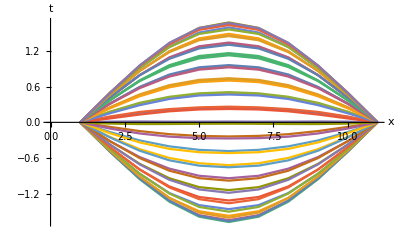

```mathematica
ListLinePlot[func3[50],AxesLabel->{"x","t"}]
```

```mathematica
Animate[ListLinePlot[func3[n]⟦-1⟧,PlotRange->{-3,3}],{n,2,400}]
```